## Code to detect if inside polygon by Shreyas & Arifa, Jan 20, 2019

InitializationObjects

```mathematica
pointinregionREV1[points_,{x_,y_}]:=Module[{a,b,c},
(*a = Δy, b = Δx, *)
a=Table[points⟦i,2⟧-points⟦i+1,2⟧,{i,1,Length[points]-1,1}];
b=Table[points⟦i+1,1⟧-points⟦i,1⟧,{i,1,Length[points]-1,1}];
c=Table[(points⟦i,1⟧*points⟦i+1,2⟧)-(points⟦i+1,1⟧*points⟦i,2⟧),{i,1,Length[points]-1,1}];
(*         For all, is it true that  (     ax + by + c ≤ 0 )*)
And@@((#>0)&/@Chop[((#*x)&/@a)+((#*y)&/@b)+(#&/@c)])
]
```

```mathematica
pointinregionREV2[points_,{x_,y_}]:=
(*a = Δy, b = Δx, *)
(*points=AppendTo[points,First[points]];*)
And@@Table[((x*(points⟦i,2⟧-points⟦i+1,2⟧)) +( y*(points⟦i+1,1⟧-points⟦i,1⟧) )+  (points⟦i,1⟧*points⟦i+1,2⟧)-(points⟦i+1,1⟧*points⟦i,2⟧))>0,{i,1,Length[points]-1,1}]
```

```mathematica
pointinregionREV3[poly_,{x_,y_}]:=Module[{},And@@((#<0)&/@(x(#⟦;;,2⟧-RotateRight[#]⟦;;,2⟧) +  y(RotateRight[#]⟦;;,1⟧-#⟦;;,1⟧) +  #⟦;;,1⟧RotateRight[#]⟦;;,2⟧-RotateRight[#]⟦;;,1⟧#⟦;;,2⟧&@poly))]
```

```mathematica
(*winding[] and testpoint[] from https://mathematica.stackexchange.com/questions/9405/how-to-check-if-a-2d-point-is-in-a-polygon *)
winding[poly_,pt_]:=Round[(Total@Mod[(#-RotateRight[#])&@(ArcTan@@(pt-#)&/@poly),2 Pi,-Pi]/2/Pi)]
(*true if pt  is inside polygon*)
testpoint[poly_,pt_]:=Round[(Total@Mod[(#-RotateRight[#])&@(ArcTan@@(pt-#)&/@poly),2 Pi,-Pi]/2/Pi)]≠0
```

### Assignment: which is faster? Your point_in_region, or the winding calculation Using Timing. Generate a polygon Generate 10,000 random points Evaluate each point if it is in or out Compare

Demo code

```mathematica
Manipulate[Module[{g,oldr,bound,convexShape,pts,points,result1,result2},
(*Module[{bound,convexShape},*)
g=0;
oldr={0,0};
bound=5CirclePoints[4];
convexShape=(o+ #)&/@CirclePoints[n];
pts = RandomPoint[Polygon[bound],1000];
result1=Timing[testpoint[convexShape,#]&/@pts;];
result2=Timing[pointinregionREV2[convexShape,#]&/@pts;];
(*CellPrint["Winding Method Time ="];
CellPrint[result1⟦1⟧];
CellPrint["Book Method Time ="];
CellPrint[result2⟦1⟧];*)
(*Print[r];*)
Graphics[
{EdgeForm[Thin]
,{LightYellow
,Polygon[bound]}
,{LightBlue
,Polygon[convexShape]},
{Red,Point[pts]}
(*If[pointinregionREV2[points,r]
,{Red,Point[r]},{Green,Point[r]}]*)
}
]](*]*)
,{{n,3,"Number of sides"},3,9,1}
(*,{{r,{-2,2}},{-5/(√2),-5/(√2)},{5/(√2),5/(√2)},Locator}*)
,{{o,{2,1}},{-5/(√2),-5/(√2)},{5/(√2),5/(√2)},Locator}
]
```

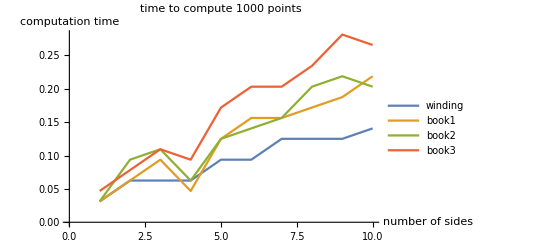

```mathematica
Module[{o,g,n,oldr,bound,pts,time3Tests,result1,result2,result3,result4},
g=0;
o={2,1};
n=3;(*"Number of sides"*)
oldr={0,0};
bound=5CirclePoints[4];
pts = RandomPoint[Polygon[bound],1000];
time3Tests = Table[
convexShape=(o+ #)&/@CirclePoints[n];
result1=Timing[testpoint[convexShape,#]&/@pts];
result4=Timing[pointinregionREV1[convexShape,#]&/@pts];
result2=Timing[pointinregionREV2[convexShape,#]&/@pts];
result3=Timing[pointinregionREV3[convexShape,#]&/@pts];
{First[result1],First[result2],First[result3],First[result4]},{n,3,12,1}];
ListLinePlot[Transpose@time3Tests,PlotLegends->{"winding","book1","book2","book3"},AxesLabel->{"number of sides","computation time"},PlotLabel->"time to compute 1000 points"]
]
```

```mathematica
s={{1,1},{2,2}}
```

{{1,1},{2,2}}

```mathematica
And&@s
```

And